{{7,8,2,7,6},{5,6,8,8,0},{3,7,2,7,2},{6,0,9,2,8},{3,9,0,3,5}}

{{7},{1},{6},{9},{2}}

(7 | 8 | 2 | 7 | 6
5 | 6 | 8 | 8 | 0
3 | 7 | 2 | 7 | 2
6 | 0 | 9 | 2 | 8
3 | 9 | 0 | 3 | 5)

(7
1
6
9
2)

{{0,4,6,0,7},{5,9,7,7,2},{3,3,7,1,1},{2,9,5,7,2},{1,3,4,4,0}}

{{-9379/6579},{-6977/6579},{-1499/6579},{104/51},{4256/2193}}

{{-160,584,-192,-568,128},{-384,384,48,-600,-456},{374,-427,-219,326,146},{346,-293,-189,322,550},{-246,87,-9,-126,6}}

3

15 cofactors

2617872224256

```mathematica
A = {{1, 2, 3, 3}, {3, 4, 4, 5}, {2, 2, 1, 2}, {□, □, □, □}}
```

{{y[t]→-1/23 ⅇ^-t (23 Cos[√23 t]+√23 Sin[√23 t])}}

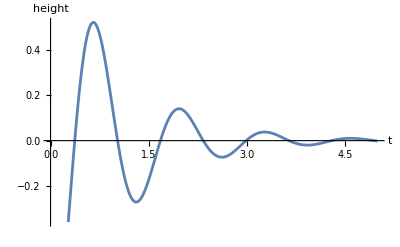

```mathematica
(*ex9*)
m = 1/4; y0 = -1; v0 = 0; a = 1/2; k = 6;
solution = DSolve[{m y''[t]+a y'[t]+k y[t] == 0, y'[0] == v0, y[0] == y0},y[t],t]
height[t_] := solution[[1,1,2]];
Plot[height[t],{t,0,5},AxesLabel->{"t","height"}]
```